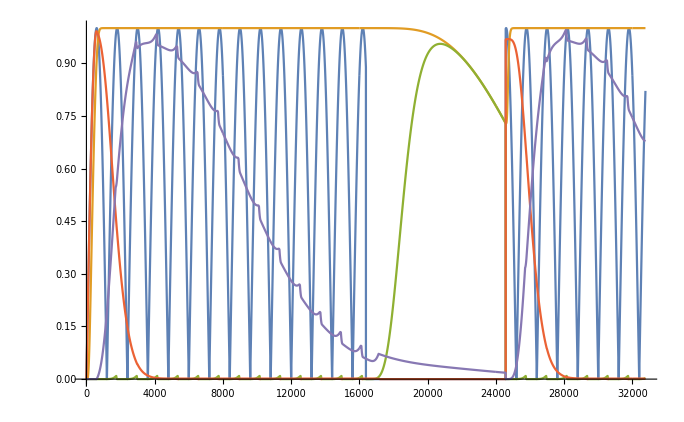

```mathematica
releaseOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]


attackOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]


EnvelopeProcessSeparateTriple[X_]:=Module[{fMultiplier,Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
attackFc =200;
releaseFc = 2.7;
Q=0.5;
fMultiplier = 1.5;

output =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate]; 


output
]

ReleaseEnvelope[X_]:=Module[{fMultiplier,Q,attackFc,releaseFc,sampleRate,releaseFilteredSlow, releaseFilteredFast,fastFc,output},
sampleRate = 48000;
attackFc =200;
releaseFc = 1.5;
Q=0.5;
fMultiplier = 2.7;
fastFc = 10;

(* filter this four times because with the higher frequency on the release envelope, the control signal leaks *)
releaseFilteredFast =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,fastFc fMultiplier,Q,sampleRate],
fastFc fMultiplier,Q,sampleRate],
fastFc fMultiplier,Q,sampleRate],
fastFc fMultiplier,Q,sampleRate]; 

releaseFilteredSlow =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate]; 

releaseFilteredSlow - releaseFilteredFast 
]

AttackEnvelope[X_]:=Module[{fMultiplier,Q, attackSlowFc,releaseFc,sampleRate,attackFilteredSlow, attackFilteredFast,output},
sampleRate = 48000;
attackSlowFc = 20;
releaseFc = 7;
Q=0.5;
fMultiplier = 1.5;

attackFilteredFast =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
X,
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate]; 

attackFilteredSlow =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
attackFilteredFast,
attackSlowFc fMultiplier,Q,sampleRate],
attackSlowFc fMultiplier,Q,sampleRate],
attackSlowFc fMultiplier,Q,sampleRate]; 

attackFilteredFast -attackFilteredSlow
]

AfterAttackEnvelope[X_]:=Module[{fMultiplier,Q,attackFastFc, attackSlowFc,releaseFc,releaseFc2,sampleRate,attackFilteredSlow, attackFilteredFast,attackEnvSlowRelease,attackEnv},
sampleRate = 48000;
attackSlowFc = 20;
releaseFc = 15;
releaseFc2 = 3.5;
Q=0.5;
fMultiplier = 1.5;

attackFilteredFast =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate];

attackFilteredSlow =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
attackFilteredFast,
attackSlowFc fMultiplier,Q,sampleRate],
attackSlowFc fMultiplier,Q,sampleRate],
attackSlowFc fMultiplier,Q,sampleRate]; 

attackEnv =attackFilteredFast -attackFilteredSlow ;

attackEnvSlowRelease =
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
attackEnv,
releaseFc2 fMultiplier,Q,sampleRate],
releaseFc2 fMultiplier,Q,sampleRate],
releaseFc2 fMultiplier,Q,sampleRate];

attackEnvSlowRelease -attackEnv
]

sampleRate = 48000;
length = 2^15;
input = Table[0Sin[151 2π N[x]]+Sin[20 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0;

 ListLinePlot[{Abs[input],EnvelopeProcessSeparateTriple[Abs[input]],ReleaseEnvelope[Abs[input]],AttackEnvelope[Abs[input]],AfterAttackEnvelope[Abs[input]]}]
```

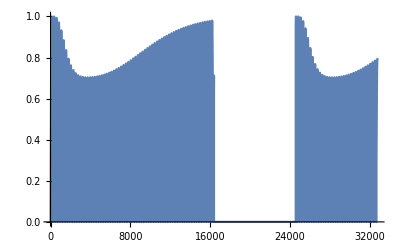

```mathematica
ListLinePlot[{Abs[input]*(1.0-0.3AfterAttackEnvelope[Abs[input]])}]
```

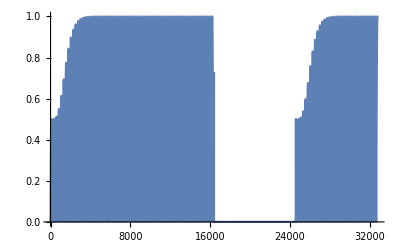

```mathematica
ListLinePlot[{(Abs[input](1.0 -0.5AttackEnvelope[Abs[input]]))},PlotRange->All]
```